## 3 sites

## Stationary points and their positions

### Hamiltonian

```mathematica
hamiltonian[j_,u_,p1_,q1_,p2_,q2_]:=-j((q1+q2)√(2  - q1^2-q2^2-p1^2-p2^2) + q1 q2 + p1 p2 ) + u/4((2  - q1^2-q2^2-p1^2-p2^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2)
```

### Numerical calculation

#### Inicialisation

```mathematica
u=1;
stepj=0.001;
error=10^-5;
numGuess=1000;
```

#### Equations

```mathematica
variables={p1,q1,p2,q2}
derivatives=FullSimplify/@D[hamiltonian[j,u,p1,q1,p2,q2],#]&/@variables
equations=(#==0)&/@derivatives
ns=(#1^2+#2^2)&@@@Partition[variables,2]
dim=Length[variables]
```

{p1,q1,p2,q2}

{-j p2+(j p1 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+p1 (-2+2 p1^2+p2^2+2 q1^2+q2^2),q1 (-2+2 p1^2+p2^2+2 q1^2+q2^2)-j (q2-(q1 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+√(2-p1^2-p2^2-q1^2-q2^2)),-j p1+(j p2 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+p2 (-2+p1^2+2 p2^2+q1^2+2 q2^2),q2 (-2+p1^2+2 p2^2+q1^2+2 q2^2)-j (q1-(q2 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+√(2-p1^2-p2^2-q1^2-q2^2))}

{-j p2+(j p1 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+p1 (-2+2 p1^2+p2^2+2 q1^2+q2^2)==0,q1 (-2+2 p1^2+p2^2+2 q1^2+q2^2)-j (q2-(q1 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+√(2-p1^2-p2^2-q1^2-q2^2))==0,-j p1+(j p2 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+p2 (-2+p1^2+2 p2^2+q1^2+2 q2^2)==0,q2 (-2+p1^2+2 p2^2+q1^2+2 q2^2)-j (q1-(q2 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+√(2-p1^2-p2^2-q1^2-q2^2))==0}

{p1^2+q1^2,p2^2+q2^2}

4

#### Parallel calculation

```mathematica
LaunchKernels[12];
```

```mathematica
result=ParallelTable[Module[{guess,solutions,t,sol},
solutions={};
t=Timing[Do[guess=RandomReal[{-√2,√2},dim];
If[guess.guess<2,Quiet[sol=Chop[FindRoot[equations,Transpose[{variables, guess}]]]];
If[Total[Abs[derivatives]/.sol]<error&&Total[Abs[Im[derivatives]]/.sol]==0,
solutions=Append[solutions,sol]]],{i,1,numGuess} ];
solutions=Union[solutions,SameTest->(Norm[Values[#1]-Values[#2]]<error&)]][[1]];{
{j,t,Length[solutions]},
Tuples[{{j},hamiltonian[j,u,p1,q1,p2,q2]/.solutions}],
Tuples[{{j},#/. solutions}]&/@variables,
Tuples[{{j},#/. solutions}]&/@ns}],{j,-1,1,stepj},Method->"FinestGrained"];
```

#### Reordering

```mathematica
tvar=Table[{},{dim}];
tn=Table[{},{dim/2}];
h={};
```

```mathematica
Do[
h=Append[h,item[[2]]];
Do[tvar[[i]]=Append[tvar[[i]],item[[3,i]]],{i,1,dim}];
Do[tn[[i]]=Append[tn[[i]],item[[4,i]]],{i,1,dim/2}],{item,result}];
```

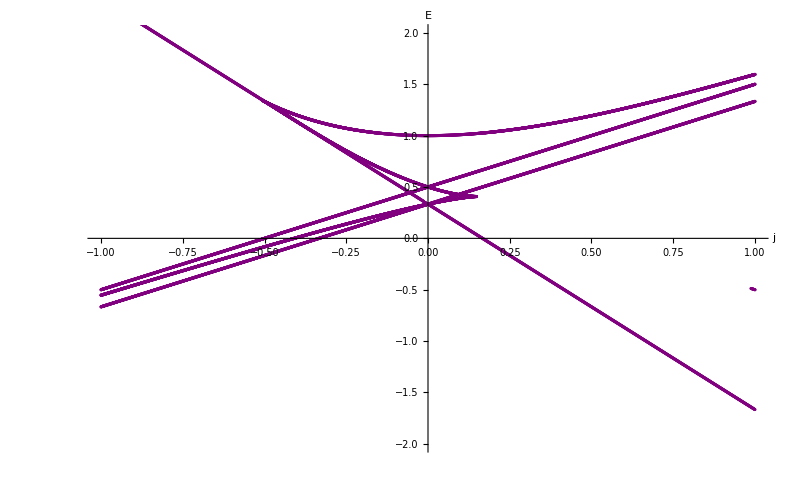

```mathematica
ListPlot[h,PlotRange->{-2,2},PlotStyle->Purple,AxesLabel->{"j","E"},ImageSize->800]
```

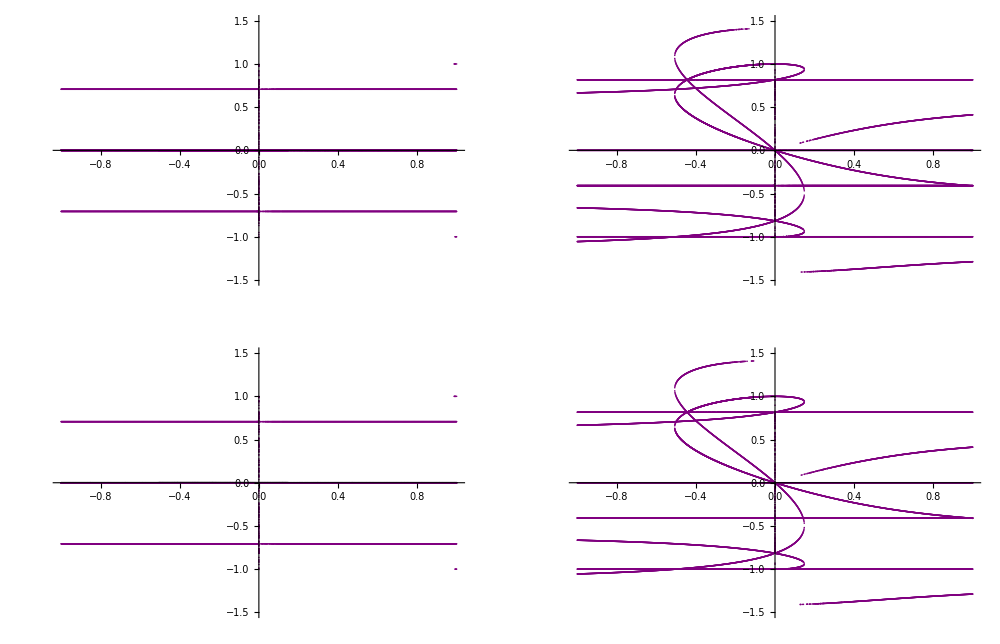

```mathematica
plots=ListPlot[#,PlotRange->{-1.5,1.5},PlotStyle->Purple]&/@tvar;
GraphicsGrid[Partition[plots,2],ImageSize->1000]
```

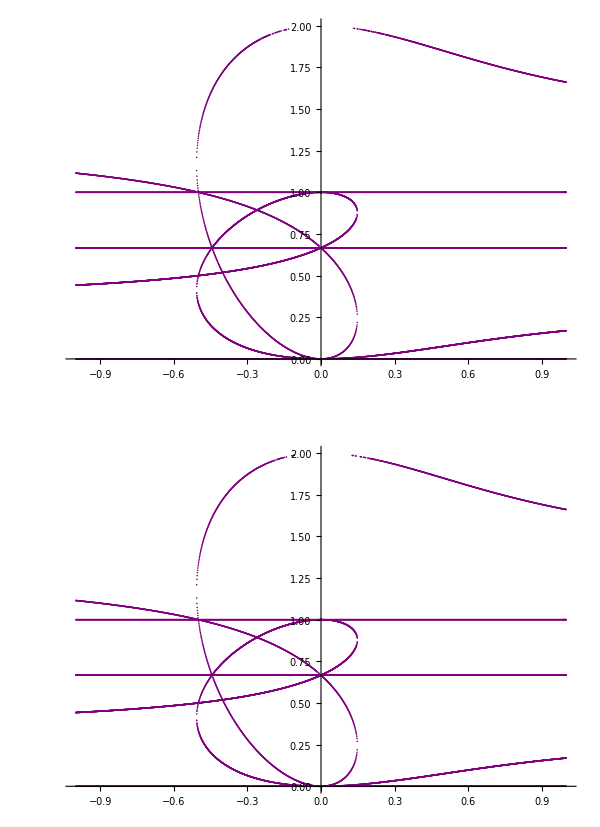

```mathematica
plots=ListPlot[#,PlotStyle->Purple,PlotRange->{0,2}]&/@tn;
GraphicsGrid[Partition[plots,1],ImageSize->600]
```

#### Saving

```mathematica
Export["d:\\h.txt",N[h],"CSV"];
```

## 4 sites

## Stationary points and their positions

### Hamiltonian

```mathematica
hamiltonian[j_,u_,p1_,q1_,p2_,q2_,p3_,q3_]:=-j((q1+q3)√(2  - q1^2-q2^2-q3^2-p1^2-p2^2-p3^2) + q1 q2 + p1 p2 +  q2 q3 + p2 p3 ) + u/4((2  - q1^2-q2^2-q3^2-p1^2-p2^2-p3^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2+(q3^2+p3^2)^2)
```

### Numerical calculation

#### Inicialisation

```mathematica
u=1;
stepj=0.001;
error=10^-5;
numGuess=5000;
```

#### Equations

```mathematica
variables={p1,q1,p2,q2,p3,q3}
derivatives=FullSimplify/@D[hamiltonian[j,u,p1,q1,p2,q2,p3,q3],#]&/@variables
equations=(#==0)&/@derivatives
ns=(#1^2+#2^2)&@@@Partition[variables,2]
dim=Length[variables]
```

{p1,q1,p2,q2,p3,q3}

{-j p2+(j p1 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))+p1 (-2+2 p1^2+p2^2+p3^2+2 q1^2+q2^2+q3^2),-j q2+q1 (-2+2 p1^2+p2^2+p3^2+2 q1^2+q2^2+q3^2)+(j (-2+p1^2+p2^2+p3^2+2 q1^2+q2^2+q1 q3+q3^2))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2)),p2 (-2+p1^2+2 p2^2+p3^2+q1^2+2 q2^2+q3^2)-j (p1+p3-(p2 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))),q2 (-2+p1^2+2 p2^2+p3^2+q1^2+2 q2^2+q3^2)-j (q1+q3-(q2 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))),-j p2+(j p3 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))+p3 (-2+p1^2+p2^2+2 p3^2+q1^2+q2^2+2 q3^2),-j q2+q3 (-2+p1^2+p2^2+2 p3^2+q1^2+q2^2+2 q3^2)+(j (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q1 q3+2 q3^2))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))}

{-j p2+(j p1 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))+p1 (-2+2 p1^2+p2^2+p3^2+2 q1^2+q2^2+q3^2)==0,-j q2+q1 (-2+2 p1^2+p2^2+p3^2+2 q1^2+q2^2+q3^2)+(j (-2+p1^2+p2^2+p3^2+2 q1^2+q2^2+q1 q3+q3^2))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))==0,p2 (-2+p1^2+2 p2^2+p3^2+q1^2+2 q2^2+q3^2)-j (p1+p3-(p2 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2)))==0,q2 (-2+p1^2+2 p2^2+p3^2+q1^2+2 q2^2+q3^2)-j (q1+q3-(q2 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2)))==0,-j p2+(j p3 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))+p3 (-2+p1^2+p2^2+2 p3^2+q1^2+q2^2+2 q3^2)==0,-j q2+q3 (-2+p1^2+p2^2+2 p3^2+q1^2+q2^2+2 q3^2)+(j (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q1 q3+2 q3^2))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))==0}

{p1^2+q1^2,p2^2+q2^2,p3^2+q3^2}

6

#### Parallel calculation

```mathematica
LaunchKernels[12];
```

```mathematica
result=ParallelTable[Module[{guess,solutions,t,sol},
solutions={};
t=Timing[Do[guess=RandomReal[{-√2,√2},dim];
If[guess.guess<2,Quiet[sol=Chop[FindRoot[equations,Transpose[{variables, guess}]]]];
If[Total[Abs[derivatives]/.sol]<error&&Total[Abs[Im[derivatives]]/.sol]==0,
solutions=Append[solutions,sol]]],{i,1,numGuess} ];
solutions=Union[solutions,SameTest->(Norm[Values[#1]-Values[#2]]<error&)]][[1]];{
{j,t,Length[solutions]},
Tuples[{{j},hamiltonian[j,u,p1,q1,p2,q2,p3,q3]/.solutions}],
Tuples[{{j},#/. solutions}]&/@variables,
Tuples[{{j},#/. solutions}]&/@ns}],{j,-1,1,stepj},Method->"FinestGrained"];
```

#### Reordering

```mathematica
tvar=Table[{},{dim}];
tn=Table[{},{dim/2}];
h={};
```

```mathematica
Do[
h=Append[h,item[[2]]];
Do[tvar[[i]]=Append[tvar[[i]],item[[3,i]]],{i,1,dim}];
Do[tn[[i]]=Append[tn[[i]],item[[4,i]]],{i,1,dim/2}],{item,result}];
```

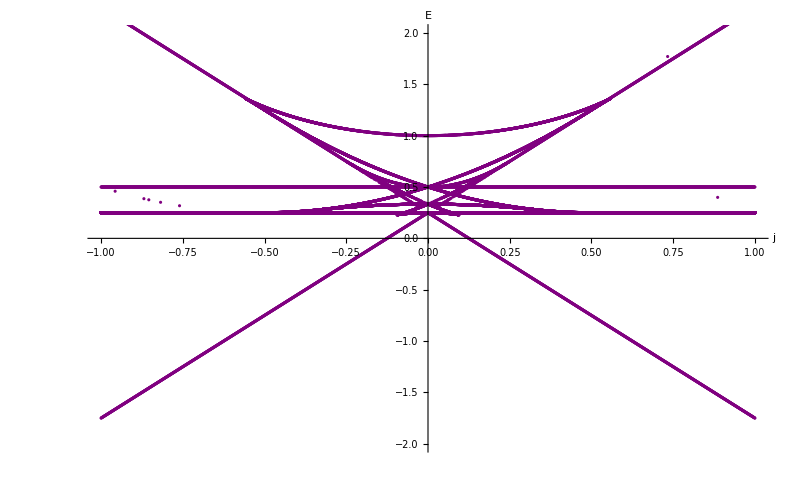

```mathematica
ListPlot[h,PlotRange->{-2,2},PlotStyle->Purple,AxesLabel->{"j","E"},ImageSize->800]
```

```mathematica
plots=ListPlot[#,PlotRange->{-1.5,1.5},PlotStyle->Purple]&/@tvar;
GraphicsGrid[Partition[plots,2],ImageSize->1200]
```

-Graphics-

```mathematica
ListPlot[Flatten[tn,1],PlotStyle->Purple,PlotRange->{0,2},ImageSize->600]
```

-Graphics-

#### Saving

```mathematica
Export["d:\\h.txt",N[h],"CSV"];
```

## 5 sites

## Stationary points and their positions

### Hamiltonian

```mathematica
hamiltonian[j_,u_,p1_,q1_,p2_,q2_,p3_,q3_,p4_,q4_]:=-j((q1+q4)√(2  - q1^2-q2^2-q3^2-q4^2-p1^2-p2^2-p3^2-p4^2) + q1 q2 + p1 p2 +  q2 q3 + p2 p3 +q3 q4+p3 p4) + u/4((2  - q1^2-q2^2-q3^2-q4^2-p1^2-p2^2-p3^2-p4^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2+(q3^2+p3^2)^2+(q4^2+p4^2)^2)
```

### Numerical calculation

#### Inicialisation

```mathematica
u=1;
stepj=0.001;
error=10^-5;
numGuess=10000;
```

#### Equations

```mathematica
variables={p1,q1,p2,q2,p3,q3,p4,q4}
derivatives=FullSimplify/@D[hamiltonian[j,u,p1,q1,p2,q2,p3,q3,p4,q4],#]&/@variables
equations=(#==0)&/@derivatives
ns=(#1^2+#2^2)&@@@Partition[variables,2]
dim=Length[variables]
```

{p1,q1,p2,q2,p3,q3,p4,q4}

{-j p2+(j p1 (q1+q4))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2))+p1 (-2+2 p1^2+p2^2+p3^2+p4^2+2 q1^2+q2^2+q3^2+q4^2),-j q2+q1 (-2+2 p1^2+p2^2+p3^2+p4^2+2 q1^2+q2^2+q3^2+q4^2)+(j (-2+p1^2+p2^2+p3^2+p4^2+2 q1^2+q2^2+q3^2+q1 q4+q4^2))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2)),p2 (-2+p1^2+2 p2^2+p3^2+p4^2+q1^2+2 q2^2+q3^2+q4^2)-j (p1+p3-(p2 (q1+q4))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2))),q2 (-2+p1^2+2 p2^2+p3^2+p4^2+q1^2+2 q2^2+q3^2+q4^2)-j (q1+q3-(q2 (q1+q4))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2))),p3 (-2+p1^2+p2^2+2 p3^2+p4^2+q1^2+q2^2+2 q3^2+q4^2)-j (p2+p4-(p3 (q1+q4))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2))),q3 (-2+p1^2+p2^2+2 p3^2+p4^2+q1^2+q2^2+2 q3^2+q4^2)-j (q2+q4-(q3 (q1+q4))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2))),-j p3+(j p4 (q1+q4))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2))+p4 (-2+p1^2+p2^2+p3^2+2 p4^2+q1^2+q2^2+q3^2+2 q4^2),-j q3+q4 (-2+p1^2+p2^2+p3^2+2 p4^2+q1^2+q2^2+q3^2+2 q4^2)+(j (-2+p1^2+p2^2+p3^2+p4^2+q1^2+q2^2+q3^2+q1 q4+2 q4^2))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2))}

{-j p2+(j p1 (q1+q4))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2))+p1 (-2+2 p1^2+p2^2+p3^2+p4^2+2 q1^2+q2^2+q3^2+q4^2)==0,-j q2+q1 (-2+2 p1^2+p2^2+p3^2+p4^2+2 q1^2+q2^2+q3^2+q4^2)+(j (-2+p1^2+p2^2+p3^2+p4^2+2 q1^2+q2^2+q3^2+q1 q4+q4^2))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2))==0,p2 (-2+p1^2+2 p2^2+p3^2+p4^2+q1^2+2 q2^2+q3^2+q4^2)-j (p1+p3-(p2 (q1+q4))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2)))==0,q2 (-2+p1^2+2 p2^2+p3^2+p4^2+q1^2+2 q2^2+q3^2+q4^2)-j (q1+q3-(q2 (q1+q4))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2)))==0,p3 (-2+p1^2+p2^2+2 p3^2+p4^2+q1^2+q2^2+2 q3^2+q4^2)-j (p2+p4-(p3 (q1+q4))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2)))==0,q3 (-2+p1^2+p2^2+2 p3^2+p4^2+q1^2+q2^2+2 q3^2+q4^2)-j (q2+q4-(q3 (q1+q4))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2)))==0,-j p3+(j p4 (q1+q4))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2))+p4 (-2+p1^2+p2^2+p3^2+2 p4^2+q1^2+q2^2+q3^2+2 q4^2)==0,-j q3+q4 (-2+p1^2+p2^2+p3^2+2 p4^2+q1^2+q2^2+q3^2+2 q4^2)+(j (-2+p1^2+p2^2+p3^2+p4^2+q1^2+q2^2+q3^2+q1 q4+2 q4^2))/(√(2-p1^2-p2^2-p3^2-p4^2-q1^2-q2^2-q3^2-q4^2))==0}

{p1^2+q1^2,p2^2+q2^2,p3^2+q3^2,p4^2+q4^2}

8

#### Parallel calculation

```mathematica
LaunchKernels[12];
```

```mathematica
result=ParallelTable[Module[{guess,solutions,t,sol},
solutions={};
t=Timing[Do[guess=RandomReal[{-√2,√2},dim];
If[guess.guess<2,Quiet[sol=Chop[FindRoot[equations,Transpose[{variables, guess}]]]];
If[Total[Abs[derivatives]/.sol]<error&&Total[Abs[Im[derivatives]]/.sol]==0,
solutions=Append[solutions,sol]]],{i,1,numGuess} ];
solutions=Union[solutions,SameTest->(Norm[Values[#1]-Values[#2]]<error&)]][[1]];{
{j,t,Length[solutions]},
Tuples[{{j},hamiltonian[j,u,p1,q1,p2,q2,p3,q3,p4,q4]/.solutions}],
Tuples[{{j},#/. solutions}]&/@variables,
Tuples[{{j},#/. solutions}]&/@ns}],{j,-1,1,stepj},Method->"FinestGrained"];
```

#### Reordering

```mathematica
tvar=Table[{},{dim}];
tn=Table[{},{dim/2}];
h={};
```

```mathematica
Do[
h=Append[h,item[[2]]];
Do[tvar[[i]]=Append[tvar[[i]],item[[3,i]]],{i,1,dim}];
Do[tn[[i]]=Append[tn[[i]],item[[4,i]]],{i,1,dim/2}],{item,result}];
```

```mathematica
ListPlot[h,PlotRange->{-2,2},PlotStyle->Purple,AxesLabel->{"j","E"},ImageSize->800]
```

-Graphics-

```mathematica
ListPlot[Flatten[tn,1],PlotStyle->Purple,PlotRange->{0,2},ImageSize->600]
```

-Graphics-

#### Saving

```mathematica
Export["d:\\h.txt",N[h],"CSV"];
```

## 6 sites

## Stationary points and their positions

### Hamiltonian

```mathematica
hamiltonian[j_,u_,p1_,q1_,p2_,q2_,p3_,q3_,p4_,q4_,p5_,q5_]:=-j((q1+q5)√(2  - q1^2-q2^2-q3^2-q4^2-q5^2-p1^2-p2^2-p3^2-p4^2-p5^2) + q1 q2 + p1 p2 +  q2 q3 + p2 p3 +q3 q4+p3 p4+q4 q5+p4 p5) + u/4((2  - q1^2-q2^2-q3^2-q4^2-q5^2-p1^2-p2^2-p3^2-p4^2-p5^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2+(q3^2+p3^2)^2+(q4^2+p4^2)^2+(q5^2+p5^2)^2)
```

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->20,PointSize->0.002,GridLinesStyle->Thick},ImageSize->800,AxesStyle->Thick];
```

### Numerical calculation

#### Inicialisation

```mathematica
u=1;
stepj=0.001;
error=10^-5;
numGuess=100000;
```

#### Equations

```mathematica
variables={p1,q1,p2,q2,p3,q3,p4,q4,p5,q5}
derivatives=FullSimplify/@D[hamiltonian[j,u,p1,q1,p2,q2,p3,q3,p4,q4,p5,q5],#]&/@variables
equations=(#==0)&/@derivatives
ns=(#1^2+#2^2)&@@@Partition[variables,2]
dim=Length[variables]
```

{p1,q1,p2,q2,p3,q3,p4,q4,p5,q5}

{-j p2+(j p1 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2))+p1 (-2+2 p1^2+p2^2+p3^2+p4^2+p5^2+2 q1^2+q2^2+q3^2+q4^2+q5^2),-j q2+q1 (-2+2 p1^2+p2^2+p3^2+p4^2+p5^2+2 q1^2+q2^2+q3^2+q4^2+q5^2)+(j (-2+p1^2+p2^2+p3^2+p4^2+p5^2+2 q1^2+q2^2+q3^2+q4^2+q1 q5+q5^2))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2)),p2 (-2+p1^2+2 p2^2+p3^2+p4^2+p5^2+q1^2+2 q2^2+q3^2+q4^2+q5^2)-j (p1+p3-(p2 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2))),q2 (-2+p1^2+2 p2^2+p3^2+p4^2+p5^2+q1^2+2 q2^2+q3^2+q4^2+q5^2)-j (q1+q3-(q2 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2))),p3 (-2+p1^2+p2^2+2 p3^2+p4^2+p5^2+q1^2+q2^2+2 q3^2+q4^2+q5^2)-j (p2+p4-(p3 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2))),q3 (-2+p1^2+p2^2+2 p3^2+p4^2+p5^2+q1^2+q2^2+2 q3^2+q4^2+q5^2)-j (q2+q4-(q3 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2))),p4 (-2+p1^2+p2^2+p3^2+2 p4^2+p5^2+q1^2+q2^2+q3^2+2 q4^2+q5^2)-j (p3+p5-(p4 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2))),q4 (-2+p1^2+p2^2+p3^2+2 p4^2+p5^2+q1^2+q2^2+q3^2+2 q4^2+q5^2)-j (q3+q5-(q4 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2))),-j p4+(j p5 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2))+p5 (-2+p1^2+p2^2+p3^2+p4^2+2 p5^2+q1^2+q2^2+q3^2+q4^2+2 q5^2),-j q4+q5 (-2+p1^2+p2^2+p3^2+p4^2+2 p5^2+q1^2+q2^2+q3^2+q4^2+2 q5^2)+(j (-2+p1^2+p2^2+p3^2+p4^2+p5^2+q1^2+q2^2+q3^2+q4^2+q1 q5+2 q5^2))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2))}

{-j p2+(j p1 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2))+p1 (-2+2 p1^2+p2^2+p3^2+p4^2+p5^2+2 q1^2+q2^2+q3^2+q4^2+q5^2)==0,-j q2+q1 (-2+2 p1^2+p2^2+p3^2+p4^2+p5^2+2 q1^2+q2^2+q3^2+q4^2+q5^2)+(j (-2+p1^2+p2^2+p3^2+p4^2+p5^2+2 q1^2+q2^2+q3^2+q4^2+q1 q5+q5^2))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2))==0,p2 (-2+p1^2+2 p2^2+p3^2+p4^2+p5^2+q1^2+2 q2^2+q3^2+q4^2+q5^2)-j (p1+p3-(p2 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2)))==0,q2 (-2+p1^2+2 p2^2+p3^2+p4^2+p5^2+q1^2+2 q2^2+q3^2+q4^2+q5^2)-j (q1+q3-(q2 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2)))==0,p3 (-2+p1^2+p2^2+2 p3^2+p4^2+p5^2+q1^2+q2^2+2 q3^2+q4^2+q5^2)-j (p2+p4-(p3 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2)))==0,q3 (-2+p1^2+p2^2+2 p3^2+p4^2+p5^2+q1^2+q2^2+2 q3^2+q4^2+q5^2)-j (q2+q4-(q3 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2)))==0,p4 (-2+p1^2+p2^2+p3^2+2 p4^2+p5^2+q1^2+q2^2+q3^2+2 q4^2+q5^2)-j (p3+p5-(p4 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2)))==0,q4 (-2+p1^2+p2^2+p3^2+2 p4^2+p5^2+q1^2+q2^2+q3^2+2 q4^2+q5^2)-j (q3+q5-(q4 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2)))==0,-j p4+(j p5 (q1+q5))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2))+p5 (-2+p1^2+p2^2+p3^2+p4^2+2 p5^2+q1^2+q2^2+q3^2+q4^2+2 q5^2)==0,-j q4+q5 (-2+p1^2+p2^2+p3^2+p4^2+2 p5^2+q1^2+q2^2+q3^2+q4^2+2 q5^2)+(j (-2+p1^2+p2^2+p3^2+p4^2+p5^2+q1^2+q2^2+q3^2+q4^2+q1 q5+2 q5^2))/(√(2-p1^2-p2^2-p3^2-p4^2-p5^2-q1^2-q2^2-q3^2-q4^2-q5^2))==0}

{p1^2+q1^2,p2^2+q2^2,p3^2+q3^2,p4^2+q4^2,p5^2+q5^2}

10

#### Parallel calculation

```mathematica
LaunchKernels[12];
```

```mathematica
result=ParallelTable[Module[{guess,solutions,t,sol},
solutions={};
t=Timing[Do[guess=RandomReal[{-√2,√2},dim];
If[guess.guess<2,Quiet[sol=Chop[FindRoot[equations,Transpose[{variables, guess}]]]];
If[Total[Abs[derivatives]/.sol]<error&&Total[Abs[Im[derivatives]]/.sol]==0,
solutions=Append[solutions,sol]]],{i,1,numGuess} ];
solutions=Union[solutions,SameTest->(Norm[Values[#1]-Values[#2]]<error&)]][[1]];{
{j,t,Length[solutions]},
Tuples[{{j},hamiltonian[j,u,p1,q1,p2,q2,p3,q3,p4,q4,p5,q5]/.solutions}],
Tuples[{{j},#/. solutions}]&/@variables,
Tuples[{{j},#/. solutions}]&/@ns}],{j,-1,1,stepj},Method->"FinestGrained"];
```

#### Reordering

```mathematica
tvar=Table[{},{dim}];
tn=Table[{},{dim/2}];
h={};
```

```mathematica
Do[
h=Append[h,item[[2]]];
Do[tvar[[i]]=Append[tvar[[i]],item[[3,i]]],{i,1,dim}];
Do[tn[[i]]=Append[tn[[i]],item[[4,i]]],{i,1,dim/2}],{item,result}];
```

```mathematica
ListPlot[h,PlotRange->{-2,2},PlotStyle->Purple,AxesLabel->{"j","E"},ImageSize->800]
```

-Graphics-

```mathematica
ListPlot[Flatten[tn,1],PlotStyle->Purple,PlotRange->{0,2},ImageSize->600]
```

-Graphics-

#### Saving

```mathematica
Export["d:\\h.txt",N[h],"CSV"];
```

## 10 sites

## Stationary points and their positions

### Hamiltonian

```mathematica
hamiltonian[j_,u_,p1_,q1_,p2_,q2_,p3_,q3_,p4_,q4_,p5_,q5_,p6_,q6_,p7_,q7_,p8_,q8_,p9_,q9_]:=-j((q1+q9)√(2  - q1^2-q2^2-q3^2-q4^2-q5^2-q6^2-q7^2-q8^2-q9^2-p1^2-p2^2-p3^2-p4^2-p5^2-p6^2-p7^2-p8^2-p9^2) + q1 q2 + p1 p2 +  q2 q3 + p2 p3 +q3 q4+p3 p4+q4 q5+p4 p5+q5 q6+p5 p6+q6 q7+p6 p7+q7 q8+p7 p8+q8 q9+p8 p9) + u/4((2  - q1^2-q2^2-q3^2-q4^2-q5^2-q6^2-q7^2-q8^2-q9^2-p1^2-p2^2-p3^2-p4^2-p5^2-p6^2-p7^2-p8^2-p9^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2+(q3^2+p3^2)^2+(q4^2+p4^2)^2+(q5^2+p5^2)^2+(q6^2+p6^2)^2+(q7^2+p7^2)^2+(q8^2+p8^2)^2+(q9^2+p9^2)^2)
```

### Numerical calculation

#### Inicialisation

```mathematica
u=1;
stepj=0.001;
error=10^-5;
numGuess=100000;
```

#### Equations

```mathematica
variables={p1,q1,p2,q2,p3,q3,p4,q4,p5,q5,p6,q6,p7,q7,p8,q8,p9,q9}
derivatives=FullSimplify/@D[hamiltonian[j,u,p1,q1,p2,q2,p3,q3,p4,q4,p5,q5,p6,q6,p7,q7,p8,q8,p9,q9],#]&/@variables
equations=(#==0)&/@derivatives
ns=(#1^2+#2^2)&@@@Partition[variables,2]
dim=Length[variables]
```

#### Parallel calculation

```mathematica
LaunchKernels[12];
```

```mathematica
result=ParallelTable[Module[{guess,solutions,t,sol},
solutions={};
t=Timing[Do[guess=RandomReal[{-√2,√2},dim];
If[guess.guess<2,Quiet[sol=Chop[FindRoot[equations,Transpose[{variables, guess}]]]];
If[Total[Abs[derivatives]/.sol]<error&&Total[Abs[Im[derivatives]]/.sol]==0,
solutions=Append[solutions,sol]]],{i,1,numGuess} ];
solutions=Union[solutions,SameTest->(Norm[Values[#1]-Values[#2]]<error&)]][[1]];{
{j,t,Length[solutions]},
Tuples[{{j},hamiltonian[j,u,p1,q1,p2,q2,p3,q3,p4,q4,p5,q5,p6,q6,p7,q7,p8,q8,p9,q9]/.solutions}],
Tuples[{{j},#/. solutions}]&/@variables,
Tuples[{{j},#/. solutions}]&/@ns}],{j,-1,1,stepj},Method->"FinestGrained"];
```

#### Reordering

```mathematica
tvar=Table[{},{dim}];
tn=Table[{},{dim/2}];
h={};
```

```mathematica
Do[
h=Append[h,item[[2]]];
Do[tvar[[i]]=Append[tvar[[i]],item[[3,i]]],{i,1,dim}];
Do[tn[[i]]=Append[tn[[i]],item[[4,i]]],{i,1,dim/2}],{item,result}];
```

```mathematica
ListPlot[h,PlotRange->{-2,2},PlotStyle->Purple,AxesLabel->{"j","E"},ImageSize->800]
```

```mathematica
ListPlot[Flatten[tn,1],PlotStyle->Purple,PlotRange->{0,2},ImageSize->600]
```

#### Saving

```mathematica
Export["d:\\h.txt",N[h],"CSV"];
```